```mathematica
Ms=550000  (*Saturation in A/m*)
```

```mathematica
550000
```

```mathematica
K=35000 (*Anisotropy constant in J/m^3)
```

35000

```mathematica
m0=1.25*10^-6 (*vacuum permeability*)
```

1.25×10^-6

```mathematica
H0=24000 (*excitation field in A/m*)
```

24000

```mathematica
d=10*10^(-9) (*nanoparticle diameter in m*)
```

1/100000000

```mathematica
r=d/2 (*nanoparticle radius*)
```

1/200000000

```mathematica
V=(4/3)*Pi*r^3 (* nanoparticle volume*)
```

π/6000000000000000000000000

```mathematica
Dh=(60+d)*10^(-9) (*hydrodynamic diameter*)
```

6000000001/100000000000000000

```mathematica
Rh=Dh/2 (*hydrodynamic radius*)
```

6000000001/200000000000000000

```mathematica
Vh=(4/3)*Pi*Rh^3 (* hydrodynamic volume*)
```

(216000000108000000018000000001 π)/6000000000000000000000000000000000000000000000000000

```mathematica
T=300 (*Temperature in K*)
```

300

```mathematica
k=1.38*10^-23 (*Boltzmann constant*)
```

1.38×10^-23

```mathematica
n0=10^9 (*Larmor frequency in Hz*)
```

1000000000

```mathematica
f=765000 (*excitation frequency in Hz*)
```

765000

```mathematica
x0=(m0*(Ms^2)*V)/(3*k*T) (*Initial susceptibility*)
```

15.9409

```mathematica
tN=(1/n0)*Exp[(K*V)/(k*T)] (*Neel relaxation time*)
```

8.36432×10^-8

```mathematica
n=9*10^(-4) (*medium viscocity*)
```

9/10000

```mathematica
tB=(3*n*Vh)/(k*T) (*Brown relaxation time*)
```

0.0000737591

```mathematica
t=(tN*tB)/(tN+tB) (*total relaxation time*)
```

8.35484×10^-8

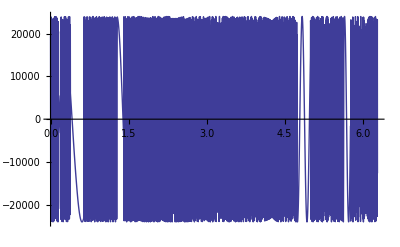

```mathematica
y1=Plot[H0*Cos[2*Pi*f*x],{x,0,2*Pi}] (*Magnetic field  plot*)
```

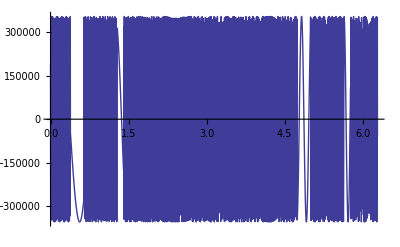

```mathematica
y2=Plot[(x0/(Sqrt[(1+(2Pi*f*t)^2)]))*H0*Cos[(2*Pi*f*x)+ArcTan[2*Pi*f*t]],{x,0,2*Pi}] (*Magnetization plot*)
```

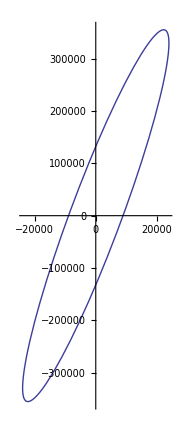

```mathematica
y3=ParametricPlot[{H0*Cos[x],(x0/(Sqrt[(1+(2Pi*f*t)^2)]))*H0*Cos[(x)+ArcTan[2*Pi*f*t]]},{x,0,2*Pi}] (*Hysteresis loop plot*)
```

```mathematica
mydatapoints=Cases[y3,Line[{x__}]->x,Infinity]
```

{{24000.,39150.},{24000.,38949.3},{23999.8,38748.3},{23999.6,38547.3},{23999.3,38346.1},{23998.9,38144.8},{23998.4,37943.3},{23997.8,37741.7},{23997.1,37539.9},{23996.4,37338.},{23995.5,37136.},{23994.6,36933.8},{23993.6,36731.5},{23992.5,36529.1},{23991.3,36326.5},{23988.6,35920.9},{23987.1,35717.9},{23985.6,35514.8},{23982.2,35108.2},{23980.4,34904.7},{23978.4,34701.},{23974.3,34293.4},{23972.2,34089.3},{23969.9,33885.2},{23965.1,33476.5},{23954.4,32657.6},{23951.5,32452.6},{23948.5,32247.5},{23942.3,31836.9},{23928.7,31014.2},{23925.1,30808.2},{23921.4,30602.2},{23913.8,30189.7},{23897.4,29363.4},{23893.1,29156.5},{23888.7,28949.5},{23879.6,28535.3},{23860.4,27705.5},{23817.7,26041.1},{23811.5,25815.1},{23805.2,25589.},{23792.2,25136.3},{23765.,24229.8},{23705.7,22411.6},{23697.9,22183.9},{23689.9,21956.1},{23673.6,21500.2},{23639.8,20587.2},{23567.3,18757.1},{23557.7,18527.9},{23548.1,18298.7},{23528.5,17840.},{23488.2,16921.7},{23402.5,15081.5},{23211.6,11389.2},{23199.6,11173.3},{23187.6,10957.3},{23163.2,10525.3},{23113.5,9660.74},{23009.9,7929.94},{22785.7,4462.97},{22771.,4246.1},{22756.2,4029.22},{22726.2,3595.42},{22665.4,2727.64},{22539.4,991.652},{22271.2,-2480.63},{22254.,-2693.35},{22236.8,-2906.05},{22202.1,-3331.44},{22131.8,-4182.04},{21987.1,-5882.48},{21682.5,-9278.82},{21662.8,-9490.83},{21643.,-9702.81},{21603.1,-10126.7},{21522.5,-10973.9},{21357.6,-12666.5},{21012.6,-16042.3},{20988.5,-16270.6},{20964.3,-16498.9},{20915.7,-16955.3},{20817.3,-17867.1},{20616.2,-19687.1},{20197.1,-23310.2},{19292.6,-30475.5},{19264.9,-30682.6},{19237.2,-30889.6},{19181.5,-31303.3},{19069.2,-32129.2},{18841.2,-33775.1},{18371.7,-37042.2},{17380.3,-43466.7},{17345.6,-43681.5},{17310.7,-43896.1},{17240.8,-44324.7},{17100.1,-45179.6},{16815.,-46879.7},{16230.8,-50240.},{15008.1,-56786.8},{14969.5,-56983.8},{14930.8,-57180.5},{14853.3,-57573.2},{14697.4,-58355.7},{14382.8,-59908.7},{13741.9,-62965.6},{12416.,-68870.8},{12376.5,-69038.6},{12336.9,-69206.1},{12257.7,-69540.4},{12098.8,-70205.8},{11778.8,-71524.2},{11130.4,-74110.},{9802.83,-79069.1},{9757.16,-79232.},{9711.45,-79394.6},{9619.91,-79718.7},{9436.33,-80362.8},{9067.22,-81634.1},{8321.53,-84108.3},{6803.25,-88773.7},{6758.47,-88904.},{6713.67,-89034.},{6623.98,-89292.8},{6444.3,-89806.5},{6083.79,-90817.6},{5358.44,-92773.5},{5312.93,-92892.8},{5267.39,-93011.7},{5176.26,-93248.5},{4993.77,-93717.9},{4627.9,-94639.6},{3892.87,-96414.},{3847.71,-96519.7},{3802.53,-96625.},{3712.13,-96834.7},{3531.17,-97249.7},{3168.64,-98062.8},{2441.47,-99620.4},{2395.94,-99714.7},{2350.4,-99808.7},{2259.29,-99995.4},{2076.98,-100365.},{1712.02,-101085.},{980.972,-102456.},{931.357,-102546.},{881.738,-102635.},{782.489,-102812.},{583.953,-103160.},{186.774,-103836.},{-607.629,-105101.},{-657.266,-105176.},{-706.9,-105251.},{-806.159,-105400.},{-1004.63,-105691.},{-1401.37,-106252.},{-2193.57,-107286.},{-2239.7,-107342.},{-2285.83,-107399.},{-2378.05,-107510.},{-2562.39,-107728.},{-2930.61,-108145.},{-2976.59,-108195.},{-3022.56,-108245.},{-3114.46,-108343.},{-3298.12,-108535.},{-3664.85,-108900.},{-3710.63,-108944.},{-3756.4,-108987.},{-3847.89,-109073.},{-4030.71,-109239.},{-4395.6,-109552.},{-4441.14,-109589.},{-4486.66,-109626.},{-4577.66,-109699.},{-4759.45,-109839.},{-5122.16,-110099.},{-5171.21,-110133.},{-5220.24,-110165.},{-5318.23,-110230.},{-5513.94,-110352.},{-5562.81,-110382.},{-5611.65,-110411.},{-5709.26,-110467.},{-5904.18,-110574.},{-5952.84,-110600.},{-6001.48,-110625.},{-6098.68,-110673.},{-6292.76,-110765.},{-6341.21,-110787.},{-6389.63,-110808.},{-6486.4,-110849.},{-6679.58,-110925.},{-6727.8,-110942.},{-6775.99,-110960.},{-6872.29,-110993.},{-6920.4,-111009.},{-6968.47,-111024.},{-7064.52,-111053.},{-7112.51,-111067.},{-7160.46,-111081.},{-7256.26,-111106.},{-7304.12,-111118.},{-7351.94,-111130.},{-7447.49,-111151.},{-7495.22,-111161.},{-7542.91,-111171.},{-7590.57,-111180.},{-7638.2,-111188.},{-7685.79,-111196.},{-7733.35,-111204.},{-7828.37,-111217.},{-7875.83,-111224.},{-7923.25,-111229.},{-7970.64,-111234.},{-8018.,-111239.},{-8065.31,-111243.},{-8112.6,-111247.},{-8159.85,-111250.},{-8207.06,-111253.},{-8253.37,-111255.},{-8299.65,-111257.},{-8345.9,-111258.},{-8392.1,-111259.},{-8438.28,-111259.},{-8484.42,-111259.},{-8530.52,-111258.},{-8576.58,-111257.},{-8622.61,-111256.},{-8668.61,-111253.},{-8714.56,-111251.},{-8760.48,-111248.},{-8806.37,-111245.},{-8852.21,-111241.},{-8898.02,-111236.},{-8943.79,-111231.},{-8989.53,-111226.},{-9035.22,-111220.},{-9080.88,-111214.},{-9126.5,-111207.},{-9172.08,-111200.},{-9217.62,-111192.},{-9308.58,-111176.},{-9354.01,-111166.},{-9399.39,-111157.},{-9490.04,-111136.},{-9535.31,-111125.},{-9580.54,-111114.},{-9670.86,-111090.},{-9715.97,-111077.},{-9761.03,-111064.},{-9851.03,-111036.},{-10030.5,-110974.},{-10075.3,-110957.},{-10120.,-110940.},{-10209.4,-110905.},{-10387.5,-110828.},{-10431.9,-110808.},{-10476.3,-110787.},{-10564.9,-110744.},{-10741.6,-110652.},{-11092.9,-110447.},{-11133.6,-110421.},{-11174.4,-110395.},{-11255.7,-110341.},{-11417.8,-110228.},{-11740.,-109984.},{-11780.1,-109951.},{-11820.1,-109919.},{-11900.,-109852.},{-12059.4,-109713.},{-12376.,-109417.},{-12415.4,-109378.},{-12454.7,-109339.},{-12533.2,-109260.},{-12689.7,-109095.},{-13000.4,-108748.},{-13612.7,-107976.},{-13653.7,-107921.},{-13694.7,-107864.},{-13776.5,-107750.},{-13939.3,-107516.},{-14262.2,-107025.},{-14302.3,-106962.},{-14342.3,-106898.},{-14422.1,-106769.},{-14581.1,-106505.},{-14895.9,-105955.},{-14935.,-105885.},{-14974.,-105813.},{-15051.8,-105670.},{-15206.7,-105377.},{-15513.2,-104769.},{-16113.4,-103466.},{-16147.9,-103386.},{-16182.3,-103306.},{-16250.9,-103145.},{-16387.4,-102819.},{-16657.5,-102147.},{-17185.6,-100730.},{-17218.,-100638.},{-17250.4,-100545.},{-17315.,-100360.},{-17443.4,-99984.3},{-17697.1,-99215.1},{-18191.6,-97605.2},{-18224.4,-97492.7},{-18257.2,-97379.8},{-18322.5,-97152.8},{-18452.2,-96693.6},{-18707.6,-95754.6},{-19202.4,-93795.9},{-19232.7,-93669.9},{-19262.8,-93543.5},{-19322.8,-93289.5},{-19441.8,-92776.5},{-19675.6,-91731.},{-20126.5,-89562.5},{-20153.4,-89426.1},{-20180.3,-89289.3},{-20233.7,-89014.6},{-20339.6,-88460.7},{-20547.1,-87334.9},{-20945.3,-85012.1},{-20969.4,-84863.9},{-20993.4,-84715.2},{-21041.2,-84416.9},{-21135.8,-83815.8},{-21320.6,-82596.7},{-21672.7,-80091.3},{-21692.5,-79942.5},{-21712.2,-79793.4},{-21751.5,-79494.3},{-21828.9,-78892.6},{-21979.9,-77675.2},{-22266.3,-75185.5},{-22283.5,-75027.5},{-22300.6,-74869.2},{-22334.6,-74551.8},{-22401.5,-73913.7},{-22531.5,-72624.4},{-22775.4,-69994.5},{-22791.1,-69813.9},{-22806.8,-69632.9},{-22837.8,-69270.1},{-22898.5,-68540.9},{-23015.4,-67068.2},{-23029.5,-66882.8},{-23043.5,-66697.1},{-23071.3,-66324.8},{-23125.7,-65576.8},{-23229.7,-64067.1},{-23242.2,-63877.1},{-23254.6,-63686.9},{-23279.2,-63305.5},{-23327.1,-62539.5},{-23418.1,-60994.6},{-23429.,-60800.2},{-23439.8,-60605.6},{-23461.1,-60215.7},{-23502.5,-59432.6},{-23580.4,-57854.},{-23589.1,-57668.7},{-23597.7,-57483.2},{-23614.5,-57111.6},{-23647.2,-56365.6},{-23708.2,-54863.5},{-23715.5,-54674.8},{-23722.6,-54485.9},{-23736.6,-54107.5},{-23763.5,-53348.1},{-23813.,-51819.7},{-23818.8,-51627.8},{-23824.5,-51435.6},{-23835.6,-51050.8},{-23856.7,-50278.7},{-23861.8,-50085.2},{-23866.8,-49891.6},{-23876.4,-49503.6},{-23894.6,-48725.5},{-23899.,-48530.5},{-23903.2,-48335.4},{-23911.4,-47944.5},{-23926.8,-47160.5},{-23930.4,-46964.},{-23933.9,-46767.4},{-23940.6,-46373.6},{-23953.1,-45584.},{-23955.9,-45390.},{-23958.6,-45195.9},{-23963.8,-44807.1},{-23966.3,-44612.5},{-23968.7,-44417.7},{-23973.2,-44027.7},{-23975.3,-43832.4},{-23977.3,-43637.},{-23981.2,-43245.7},{-23982.9,-43049.8},{-23984.6,-42853.7},{-23987.7,-42461.1},{-23989.1,-42264.6},{-23990.5,-42067.9},{-23991.7,-41871.1},{-23992.9,-41674.1},{-23994.,-41476.9},{-23994.9,-41279.6},{-23995.8,-41082.2},{-23996.6,-40884.6},{-23997.4,-40686.9},{-23998.,-40489.},{-23998.6,-40290.9},{-23999.,-40092.8},{-23999.4,-39894.4},{-23999.7,-39696.},{-23999.9,-39497.3},{-24000.,-39298.6},{-24000.,-39099.7},{-23999.9,-38900.6},{-23999.8,-38701.4},{-23999.5,-38502.1},{-23999.2,-38302.6},{-23998.8,-38103.},{-23998.3,-37903.2},{-23997.7,-37703.3},{-23997.,-37503.3},{-23996.3,-37303.1},{-23995.4,-37102.8},{-23994.5,-36902.4},{-23993.4,-36701.8},{-23992.3,-36501.1},{-23989.8,-36099.3},{-23988.4,-35898.2},{-23987.,-35697.},{-23983.8,-35294.1},{-23982.,-35092.5},{-23980.2,-34890.7},{-23976.3,-34486.9},{-23974.2,-34284.7},{-23972.1,-34082.5},{-23967.5,-33677.6},{-23957.2,-32866.3},{-23954.2,-32646.},{-23951.1,-32425.5},{-23944.5,-31984.1},{-23930.2,-31099.7},{-23926.4,-30878.2},{-23922.4,-30656.6},{-23914.2,-30213.1},{-23896.6,-29324.4},{-23891.9,-29101.9},{-23887.2,-28879.3},{-23877.3,-28433.8},{-23856.4,-27541.1},{-23809.7,-25750.3},{-23803.4,-25525.9},{-23797.,-25301.4},{-23783.9,-24852.2},{-23756.4,-23952.3},{-23696.6,-22147.8},{-23688.7,-21921.8},{-23680.6,-21695.7},{-23664.2,-21243.2},{-23630.3,-20337.2},{-23557.5,-18521.},{-23548.5,-18308.8},{-23539.5,-18096.5},{-23521.3,-17671.8},{-23483.7,-16821.5},{-23404.2,-15118.},{-23228.6,-11700.6},{-23216.9,-11486.6},{-23205.1,-11272.5},{-23181.2,-10844.3},{-23132.5,-9987.43},{-23030.8,-8271.91},{-22810.9,-4835.34},{-22795.2,-4602.35},{-22779.4,-4369.33},{-22747.5,-3903.25},{-22682.6,-2970.89},{-22547.9,-1105.61},{-22259.5,2625.36},{-22240.7,2858.5},{-22221.7,3091.61},{-22183.5,3557.81},{-22105.9,4490.01},{-21946.2,6353.38},{-21608.1,10074.3},{-21586.6,10302.2},{-21564.9,10530.2},{-21521.4,10985.9},{-21433.2,11896.8},{-21252.6,13716.2},{-20874.,17343.3},{-20049.4,24537.2},{-20024.1,24745.4},{-19998.6,24953.5},{-19947.6,25369.6},{-19844.5,26200.5},{-19634.9,27857.6},{-19201.9,31151.8},{-18282.,37648.9},{-18249.6,37866.8},{-18217.1,38084.4},{-18151.9,38519.3},{-18020.6,39387.},{-17754.1,41114.1},{-17206.6,44533.6},{-16054.9,51220.7},{-16020.2,51412.5},{-15985.4,51604.1},{-15915.7,51986.8},{-15775.7,52749.7},{-15492.6,54265.9},{-14915.4,57258.7},{-13718.3,63075.3},{-13680.8,63249.8},{-13643.2,63424.},{-13567.9,63771.8},{-13416.6,64464.5},{-13111.9,65838.7},{-12493.3,68541.},{-11221.9,73752.1},{-11178.,73924.1},{-11134.1,74095.8},{-11046.1,74438.2},{-10869.6,75119.3},{-10514.3,76465.9},{-9795.25,79096.2},{-8325.81,84094.5},{-8282.39,84234.8},{-8238.93,84374.8},{-8151.94,84653.9},{-7977.58,85208.2},{-7627.45,86301.7},{-6921.84,88426.7},{-5491.52,92422.4},{-5442.66,92551.7},{-5393.79,92680.6},{-5295.97,92937.1},{-5100.05,93445.3},{-4707.15,94442.1},{-3917.53,96356.1},{-3868.02,96472.2},{-3818.5,96587.8},{-3719.4,96817.9},{-3521.02,97272.8},{-3123.52,98162.3},{-2326.02,99858.8},{-2279.38,99954.4},{-2232.74,100050.},{-2139.44,100239.},{-1952.73,100613.},{-1578.96,101342.},{-830.368,102726.},{-783.546,102810.},{-736.722,102892.},{-643.064,103057.},{-455.721,103381.},{-80.9639,104011.},{668.519,105193.},{714.43,105263.},{760.338,105331.},{852.145,105468.},{1035.72,105736.},{1402.68,106253.},{2135.53,107214.},{2181.27,107271.},{2227.01,107327.},{2318.46,107438.},{2501.25,107656.},{2866.37,108074.},{3594.53,108832.},{3643.78,108880.},{3693.02,108927.},{3791.44,109020.},{3988.08,109201.},{4380.53,109540.},{4429.51,109580.},{4478.46,109620.},{4576.31,109698.},{4771.78,109848.},{5161.7,110126.},{5210.35,110159.},{5258.97,110191.},{5356.14,110254.},{5550.21,110374.},{5598.66,110403.},{5647.1,110431.},{5743.89,110487.},{5937.18,110591.},{5985.44,110616.},{6033.67,110641.},{6130.06,110689.},{6322.51,110778.},{6370.56,110799.},{6418.58,110820.},{6514.53,110860.},{6706.11,110935.},{6750.74,110951.},{6795.35,110967.},{6884.48,110997.},{6929.01,111012.},{6973.52,111026.},{7062.45,111053.},{7106.87,111066.},{7151.27,111078.},{7239.99,111102.},{7417.09,111144.},{7461.3,111154.},{7505.48,111163.},{7593.75,111180.},{7637.85,111188.},{7681.91,111196.},{7769.96,111209.},{7813.94,111216.},{7857.89,111221.},{7901.81,111227.},{7945.7,111232.},{7989.56,111236.},{8033.39,111240.},{8077.19,111244.},{8120.96,111247.},{8164.69,111250.},{8208.4,111253.},{8252.08,111255.},{8295.73,111257.},{8339.34,111258.},{8382.93,111259.},{8426.48,111259.},{8470.,111259.},{8513.49,111258.},{8556.95,111258.},{8600.37,111256.},{8643.77,111255.},{8687.13,111253.},{8730.46,111250.},{8773.75,111247.},{8817.01,111244.},{8860.24,111240.},{8903.44,111236.},{8946.6,111231.},{8989.73,111226.},{9032.83,111221.},{9075.89,111215.},{9161.91,111202.},{9204.87,111195.},{9247.79,111187.},{9333.54,111171.},{9376.36,111162.},{9419.14,111153.},{9504.6,111133.},{9550.85,111122.},{9597.05,111110.},{9689.34,111085.},{9735.41,111071.},{9781.45,111057.},{9873.39,111028.},{9919.29,111013.},{9965.15,110997.},{10056.7,110964.},{10239.4,110892.},{10284.9,110873.},{10330.4,110854.},{10421.3,110813.},{10602.5,110725.},{10647.7,110702.},{10692.8,110679.},{10782.9,110630.},{10962.6,110527.},{11007.4,110500.},{11052.2,110472.},{11141.5,110416.},{11319.6,110297.},{11364.1,110266.},{11408.4,110235.},{11497.,110171.},{11673.5,110036.},{11717.5,110002.},{11761.4,109966.},{11849.2,109894.},{12024.,109745.},{12371.2,109422.},{12413.5,109380.},{12455.8,109338.},{12540.3,109252.},{12708.6,109075.},{13042.6,108699.},{13084.1,108649.},{13125.5,108600.},{13208.2,108499.},{13373.,108293.},{13699.8,107857.},{13740.4,107800.},{13780.9,107744.},{13861.8,107628.},{14022.9,107392.},{14342.1,106898.},{14968.8,105823.},{15004.9,105757.},{15040.9,105690.},{15112.7,105556.},{15255.6,105282.},{15538.8,104716.},{16094.,103510.},{16128.2,103432.},{16162.4,103353.},{16230.5,103194.},{16366.,102871.},{16634.1,102207.},{17158.4,100806.},{17193.3,100708.},{17228.2,100609.},{17297.7,100410.},{17435.8,100007.},{17708.5,99179.7},{18238.9,97443.},{18271.4,97330.9},{18303.8,97218.3},{18368.3,96991.8},{18496.5,96533.9},{18749.,95597.9},{19238.3,93646.4},{19266.2,93529.3},{19294.,93411.9},{19349.4,93175.9},{19459.4,92699.7},{19675.7,91730.5},{20094.1,89725.5},{20119.6,89597.3},{20145.,89468.7},{20195.7,89210.6},{20296.,88690.3},{20493.,87633.6},{20872.,85456.6},{20894.6,85320.5},{20917.1,85184.1},{20961.8,84910.4},{21050.4,84359.1},{21223.9,83242.},{21556.1,80949.8},{21576.2,80804.},{21596.2,80657.9},{21636.,80364.9},{21714.6,79775.3},{21868.1,78582.2},{22159.8,76141.3},{22178.8,75973.2},{22197.8,75804.8},{22235.4,75466.9},{22309.4,74787.3},{22452.9,73412.9},{22470.4,73239.6},{22487.8,73066.1},{22522.3,72718.1},{22590.2,72018.3},{22721.3,70603.9},{22737.3,70425.8},{22753.1,70247.3},{22784.5,69889.5},{22846.2,69170.2},{22964.8,67717.5},{23183.1,64756.8},{23195.1,64581.9},{23207.,64406.8},{23230.4,64055.8},{23276.3,63350.9},{23363.9,61929.9},{23374.5,61751.3},{23385.,61572.4},{23405.6,61213.9},{23446.,60494.1},{23522.4,59043.9},{23531.6,58861.6},{23540.6,58679.1},{23558.5,58313.5},{23593.2,57579.6},{23658.4,56101.5},{23666.1,55915.8},{23673.8,55729.8},{23688.9,55357.4},{23717.9,54610.},{23771.8,53105.5},{23778.9,52894.5},{23785.8,52683.3},{23799.4,52260.2},{23825.2,51411.},{23831.4,51198.1},{23837.5,50985.},{23849.3,50558.},{23871.5,49701.2},{23876.8,49486.4},{23882.,49271.4},{23892.,48840.7},{23910.8,47976.6},{23915.2,47760.},{23919.5,47543.2},{23927.7,47109.},{23942.9,46237.8},{23946.4,46019.4},{23949.8,45800.9},{23956.3,45363.2},{23959.3,45144.},{23962.3,44924.6},{23967.9,44485.2},{23970.5,44265.2},{23973.,44044.9},{23977.7,43603.9},{23979.9,43383.},{23981.9,43162.},{23985.7,42719.3},{23987.4,42497.7},{23989.1,42275.9},{23990.6,42053.8},{23992.,41831.6},{23993.2,41609.2},{23994.4,41386.6},{23995.5,41163.8},{23996.4,40940.8},{23997.3,40717.6},{23998.,40494.2},{23998.6,40270.6},{23999.1,40046.9},{23999.5,39822.9},{23999.8,39598.8},{23999.9,39374.5},{24000.,39150.}}

```mathematica
Grid[mydatapoints]
```

24000. | 39150.
24000. | 38949.3
23999.8 | 38748.3
23999.6 | 38547.3
23999.3 | 38346.1
23998.9 | 38144.8
23998.4 | 37943.3
23997.8 | 37741.7
23997.1 | 37539.9
23996.4 | 37338.
23995.5 | 37136.
23994.6 | 36933.8
23993.6 | 36731.5
23992.5 | 36529.1
23991.3 | 36326.5
23988.6 | 35920.9
23987.1 | 35717.9
23985.6 | 35514.8
23982.2 | 35108.2
23980.4 | 34904.7
23978.4 | 34701.
23974.3 | 34293.4
23972.2 | 34089.3
23969.9 | 33885.2
23965.1 | 33476.5
23954.4 | 32657.6
23951.5 | 32452.6
23948.5 | 32247.5
23942.3 | 31836.9
23928.7 | 31014.2
23925.1 | 30808.2
23921.4 | 30602.2
23913.8 | 30189.7
23897.4 | 29363.4
23893.1 | 29156.5
23888.7 | 28949.5
23879.6 | 28535.3
23860.4 | 27705.5
23817.7 | 26041.1
23811.5 | 25815.1
23805.2 | 25589.
23792.2 | 25136.3
23765. | 24229.8
23705.7 | 22411.6
23697.9 | 22183.9
23689.9 | 21956.1
23673.6 | 21500.2
23639.8 | 20587.2
23567.3 | 18757.1
23557.7 | 18527.9
23548.1 | 18298.7
23528.5 | 17840.
23488.2 | 16921.7
23402.5 | 15081.5
23211.6 | 11389.2
23199.6 | 11173.3
23187.6 | 10957.3
23163.2 | 10525.3
23113.5 | 9660.74
23009.9 | 7929.94
22785.7 | 4462.97
22771. | 4246.1
22756.2 | 4029.22
22726.2 | 3595.42
22665.4 | 2727.64
22539.4 | 991.652
22271.2 | -2480.63
22254. | -2693.35
22236.8 | -2906.05
22202.1 | -3331.44
22131.8 | -4182.04
21987.1 | -5882.48
21682.5 | -9278.82
21662.8 | -9490.83
21643. | -9702.81
21603.1 | -10126.7
21522.5 | -10973.9
21357.6 | -12666.5
21012.6 | -16042.3
20988.5 | -16270.6
20964.3 | -16498.9
20915.7 | -16955.3
20817.3 | -17867.1
20616.2 | -19687.1
20197.1 | -23310.2
19292.6 | -30475.5
19264.9 | -30682.6
19237.2 | -30889.6
19181.5 | -31303.3
19069.2 | -32129.2
18841.2 | -33775.1
18371.7 | -37042.2
17380.3 | -43466.7
17345.6 | -43681.5
17310.7 | -43896.1
17240.8 | -44324.7
17100.1 | -45179.6
16815. | -46879.7
16230.8 | -50240.
15008.1 | -56786.8
14969.5 | -56983.8
14930.8 | -57180.5
14853.3 | -57573.2
14697.4 | -58355.7
14382.8 | -59908.7
13741.9 | -62965.6
12416. | -68870.8
12376.5 | -69038.6
12336.9 | -69206.1
12257.7 | -69540.4
12098.8 | -70205.8
11778.8 | -71524.2
11130.4 | -74110.
9802.83 | -79069.1
9757.16 | -79232.
9711.45 | -79394.6
9619.91 | -79718.7
9436.33 | -80362.8
9067.22 | -81634.1
8321.53 | -84108.3
6803.25 | -88773.7
6758.47 | -88904.
6713.67 | -89034.
6623.98 | -89292.8
6444.3 | -89806.5
6083.79 | -90817.6
5358.44 | -92773.5
5312.93 | -92892.8
5267.39 | -93011.7
5176.26 | -93248.5
4993.77 | -93717.9
4627.9 | -94639.6
3892.87 | -96414.
3847.71 | -96519.7
3802.53 | -96625.
3712.13 | -96834.7
3531.17 | -97249.7
3168.64 | -98062.8
2441.47 | -99620.4
2395.94 | -99714.7
2350.4 | -99808.7
2259.29 | -99995.4
2076.98 | -100365.
1712.02 | -101085.
980.972 | -102456.
931.357 | -102546.
881.738 | -102635.
782.489 | -102812.
583.953 | -103160.
186.774 | -103836.
-607.629 | -105101.
-657.266 | -105176.
-706.9 | -105251.
-806.159 | -105400.
-1004.63 | -105691.
-1401.37 | -106252.
-2193.57 | -107286.
-2239.7 | -107342.
-2285.83 | -107399.
-2378.05 | -107510.
-2562.39 | -107728.
-2930.61 | -108145.
-2976.59 | -108195.
-3022.56 | -108245.
-3114.46 | -108343.
-3298.12 | -108535.
-3664.85 | -108900.
-3710.63 | -108944.
-3756.4 | -108987.
-3847.89 | -109073.
-4030.71 | -109239.
-4395.6 | -109552.
-4441.14 | -109589.
-4486.66 | -109626.
-4577.66 | -109699.
-4759.45 | -109839.
-5122.16 | -110099.
-5171.21 | -110133.
-5220.24 | -110165.
-5318.23 | -110230.
-5513.94 | -110352.
-5562.81 | -110382.
-5611.65 | -110411.
-5709.26 | -110467.
-5904.18 | -110574.
-5952.84 | -110600.
-6001.48 | -110625.
-6098.68 | -110673.
-6292.76 | -110765.
-6341.21 | -110787.
-6389.63 | -110808.
-6486.4 | -110849.
-6679.58 | -110925.
-6727.8 | -110942.
-6775.99 | -110960.
-6872.29 | -110993.
-6920.4 | -111009.
-6968.47 | -111024.
-7064.52 | -111053.
-7112.51 | -111067.
-7160.46 | -111081.
-7256.26 | -111106.
-7304.12 | -111118.
-7351.94 | -111130.
-7447.49 | -111151.
-7495.22 | -111161.
-7542.91 | -111171.
-7590.57 | -111180.
-7638.2 | -111188.
-7685.79 | -111196.
-7733.35 | -111204.
-7828.37 | -111217.
-7875.83 | -111224.
-7923.25 | -111229.
-7970.64 | -111234.
-8018. | -111239.
-8065.31 | -111243.
-8112.6 | -111247.
-8159.85 | -111250.
-8207.06 | -111253.
-8253.37 | -111255.
-8299.65 | -111257.
-8345.9 | -111258.
-8392.1 | -111259.
-8438.28 | -111259.
-8484.42 | -111259.
-8530.52 | -111258.
-8576.58 | -111257.
-8622.61 | -111256.
-8668.61 | -111253.
-8714.56 | -111251.
-8760.48 | -111248.
-8806.37 | -111245.
-8852.21 | -111241.
-8898.02 | -111236.
-8943.79 | -111231.
-8989.53 | -111226.
-9035.22 | -111220.
-9080.88 | -111214.
-9126.5 | -111207.
-9172.08 | -111200.
-9217.62 | -111192.
-9308.58 | -111176.
-9354.01 | -111166.
-9399.39 | -111157.
-9490.04 | -111136.
-9535.31 | -111125.
-9580.54 | -111114.
-9670.86 | -111090.
-9715.97 | -111077.
-9761.03 | -111064.
-9851.03 | -111036.
-10030.5 | -110974.
-10075.3 | -110957.
-10120. | -110940.
-10209.4 | -110905.
-10387.5 | -110828.
-10431.9 | -110808.
-10476.3 | -110787.
-10564.9 | -110744.
-10741.6 | -110652.
-11092.9 | -110447.
-11133.6 | -110421.
-11174.4 | -110395.
-11255.7 | -110341.
-11417.8 | -110228.
-11740. | -109984.
-11780.1 | -109951.
-11820.1 | -109919.
-11900. | -109852.
-12059.4 | -109713.
-12376. | -109417.
-12415.4 | -109378.
-12454.7 | -109339.
-12533.2 | -109260.
-12689.7 | -109095.
-13000.4 | -108748.
-13612.7 | -107976.
-13653.7 | -107921.
-13694.7 | -107864.
-13776.5 | -107750.
-13939.3 | -107516.
-14262.2 | -107025.
-14302.3 | -106962.
-14342.3 | -106898.
-14422.1 | -106769.
-14581.1 | -106505.
-14895.9 | -105955.
-14935. | -105885.
-14974. | -105813.
-15051.8 | -105670.
-15206.7 | -105377.
-15513.2 | -104769.
-16113.4 | -103466.
-16147.9 | -103386.
-16182.3 | -103306.
-16250.9 | -103145.
-16387.4 | -102819.
-16657.5 | -102147.
-17185.6 | -100730.
-17218. | -100638.
-17250.4 | -100545.
-17315. | -100360.
-17443.4 | -99984.3
-17697.1 | -99215.1
-18191.6 | -97605.2
-18224.4 | -97492.7
-18257.2 | -97379.8
-18322.5 | -97152.8
-18452.2 | -96693.6
-18707.6 | -95754.6
-19202.4 | -93795.9
-19232.7 | -93669.9
-19262.8 | -93543.5
-19322.8 | -93289.5
-19441.8 | -92776.5
-19675.6 | -91731.
-20126.5 | -89562.5
-20153.4 | -89426.1
-20180.3 | -89289.3
-20233.7 | -89014.6
-20339.6 | -88460.7
-20547.1 | -87334.9
-20945.3 | -85012.1
-20969.4 | -84863.9
-20993.4 | -84715.2
-21041.2 | -84416.9
-21135.8 | -83815.8
-21320.6 | -82596.7
-21672.7 | -80091.3
-21692.5 | -79942.5
-21712.2 | -79793.4
-21751.5 | -79494.3
-21828.9 | -78892.6
-21979.9 | -77675.2
-22266.3 | -75185.5
-22283.5 | -75027.5
-22300.6 | -74869.2
-22334.6 | -74551.8
-22401.5 | -73913.7
-22531.5 | -72624.4
-22775.4 | -69994.5
-22791.1 | -69813.9
-22806.8 | -69632.9
-22837.8 | -69270.1
-22898.5 | -68540.9
-23015.4 | -67068.2
-23029.5 | -66882.8
-23043.5 | -66697.1
-23071.3 | -66324.8
-23125.7 | -65576.8
-23229.7 | -64067.1
-23242.2 | -63877.1
-23254.6 | -63686.9
-23279.2 | -63305.5
-23327.1 | -62539.5
-23418.1 | -60994.6
-23429. | -60800.2
-23439.8 | -60605.6
-23461.1 | -60215.7
-23502.5 | -59432.6
-23580.4 | -57854.
-23589.1 | -57668.7
-23597.7 | -57483.2
-23614.5 | -57111.6
-23647.2 | -56365.6
-23708.2 | -54863.5
-23715.5 | -54674.8
-23722.6 | -54485.9
-23736.6 | -54107.5
-23763.5 | -53348.1
-23813. | -51819.7
-23818.8 | -51627.8
-23824.5 | -51435.6
-23835.6 | -51050.8
-23856.7 | -50278.7
-23861.8 | -50085.2
-23866.8 | -49891.6
-23876.4 | -49503.6
-23894.6 | -48725.5
-23899. | -48530.5
-23903.2 | -48335.4
-23911.4 | -47944.5
-23926.8 | -47160.5
-23930.4 | -46964.
-23933.9 | -46767.4
-23940.6 | -46373.6
-23953.1 | -45584.
-23955.9 | -45390.
-23958.6 | -45195.9
-23963.8 | -44807.1
-23966.3 | -44612.5
-23968.7 | -44417.7
-23973.2 | -44027.7
-23975.3 | -43832.4
-23977.3 | -43637.
-23981.2 | -43245.7
-23982.9 | -43049.8
-23984.6 | -42853.7
-23987.7 | -42461.1
-23989.1 | -42264.6
-23990.5 | -42067.9
-23991.7 | -41871.1
-23992.9 | -41674.1
-23994. | -41476.9
-23994.9 | -41279.6
-23995.8 | -41082.2
-23996.6 | -40884.6
-23997.4 | -40686.9
-23998. | -40489.
-23998.6 | -40290.9
-23999. | -40092.8
-23999.4 | -39894.4
-23999.7 | -39696.
-23999.9 | -39497.3
-24000. | -39298.6
-24000. | -39099.7
-23999.9 | -38900.6
-23999.8 | -38701.4
-23999.5 | -38502.1
-23999.2 | -38302.6
-23998.8 | -38103.
-23998.3 | -37903.2
-23997.7 | -37703.3
-23997. | -37503.3
-23996.3 | -37303.1
-23995.4 | -37102.8
-23994.5 | -36902.4
-23993.4 | -36701.8
-23992.3 | -36501.1
-23989.8 | -36099.3
-23988.4 | -35898.2
-23987. | -35697.
-23983.8 | -35294.1
-23982. | -35092.5
-23980.2 | -34890.7
-23976.3 | -34486.9
-23974.2 | -34284.7
-23972.1 | -34082.5
-23967.5 | -33677.6
-23957.2 | -32866.3
-23954.2 | -32646.
-23951.1 | -32425.5
-23944.5 | -31984.1
-23930.2 | -31099.7
-23926.4 | -30878.2
-23922.4 | -30656.6
-23914.2 | -30213.1
-23896.6 | -29324.4
-23891.9 | -29101.9
-23887.2 | -28879.3
-23877.3 | -28433.8
-23856.4 | -27541.1
-23809.7 | -25750.3
-23803.4 | -25525.9
-23797. | -25301.4
-23783.9 | -24852.2
-23756.4 | -23952.3
-23696.6 | -22147.8
-23688.7 | -21921.8
-23680.6 | -21695.7
-23664.2 | -21243.2
-23630.3 | -20337.2
-23557.5 | -18521.
-23548.5 | -18308.8
-23539.5 | -18096.5
-23521.3 | -17671.8
-23483.7 | -16821.5
-23404.2 | -15118.
-23228.6 | -11700.6
-23216.9 | -11486.6
-23205.1 | -11272.5
-23181.2 | -10844.3
-23132.5 | -9987.43
-23030.8 | -8271.91
-22810.9 | -4835.34
-22795.2 | -4602.35
-22779.4 | -4369.33
-22747.5 | -3903.25
-22682.6 | -2970.89
-22547.9 | -1105.61
-22259.5 | 2625.36
-22240.7 | 2858.5
-22221.7 | 3091.61
-22183.5 | 3557.81
-22105.9 | 4490.01
-21946.2 | 6353.38
-21608.1 | 10074.3
-21586.6 | 10302.2
-21564.9 | 10530.2
-21521.4 | 10985.9
-21433.2 | 11896.8
-21252.6 | 13716.2
-20874. | 17343.3
-20049.4 | 24537.2
-20024.1 | 24745.4
-19998.6 | 24953.5
-19947.6 | 25369.6
-19844.5 | 26200.5
-19634.9 | 27857.6
-19201.9 | 31151.8
-18282. | 37648.9
-18249.6 | 37866.8
-18217.1 | 38084.4
-18151.9 | 38519.3
-18020.6 | 39387.
-17754.1 | 41114.1
-17206.6 | 44533.6
-16054.9 | 51220.7
-16020.2 | 51412.5
-15985.4 | 51604.1
-15915.7 | 51986.8
-15775.7 | 52749.7
-15492.6 | 54265.9
-14915.4 | 57258.7
-13718.3 | 63075.3
-13680.8 | 63249.8
-13643.2 | 63424.
-13567.9 | 63771.8
-13416.6 | 64464.5
-13111.9 | 65838.7
-12493.3 | 68541.
-11221.9 | 73752.1
-11178. | 73924.1
-11134.1 | 74095.8
-11046.1 | 74438.2
-10869.6 | 75119.3
-10514.3 | 76465.9
-9795.25 | 79096.2
-8325.81 | 84094.5
-8282.39 | 84234.8
-8238.93 | 84374.8
-8151.94 | 84653.9
-7977.58 | 85208.2
-7627.45 | 86301.7
-6921.84 | 88426.7
-5491.52 | 92422.4
-5442.66 | 92551.7
-5393.79 | 92680.6
-5295.97 | 92937.1
-5100.05 | 93445.3
-4707.15 | 94442.1
-3917.53 | 96356.1
-3868.02 | 96472.2
-3818.5 | 96587.8
-3719.4 | 96817.9
-3521.02 | 97272.8
-3123.52 | 98162.3
-2326.02 | 99858.8
-2279.38 | 99954.4
-2232.74 | 100050.
-2139.44 | 100239.
-1952.73 | 100613.
-1578.96 | 101342.
-830.368 | 102726.
-783.546 | 102810.
-736.722 | 102892.
-643.064 | 103057.
-455.721 | 103381.
-80.9639 | 104011.
668.519 | 105193.
714.43 | 105263.
760.338 | 105331.
852.145 | 105468.
1035.72 | 105736.
1402.68 | 106253.
2135.53 | 107214.
2181.27 | 107271.
2227.01 | 107327.
2318.46 | 107438.
2501.25 | 107656.
2866.37 | 108074.
3594.53 | 108832.
3643.78 | 108880.
3693.02 | 108927.
3791.44 | 109020.
3988.08 | 109201.
4380.53 | 109540.
4429.51 | 109580.
4478.46 | 109620.
4576.31 | 109698.
4771.78 | 109848.
5161.7 | 110126.
5210.35 | 110159.
5258.97 | 110191.
5356.14 | 110254.
5550.21 | 110374.
5598.66 | 110403.
5647.1 | 110431.
5743.89 | 110487.
5937.18 | 110591.
5985.44 | 110616.
6033.67 | 110641.
6130.06 | 110689.
6322.51 | 110778.
6370.56 | 110799.
6418.58 | 110820.
6514.53 | 110860.
6706.11 | 110935.
6750.74 | 110951.
6795.35 | 110967.
6884.48 | 110997.
6929.01 | 111012.
6973.52 | 111026.
7062.45 | 111053.
7106.87 | 111066.
7151.27 | 111078.
7239.99 | 111102.
7417.09 | 111144.
7461.3 | 111154.
7505.48 | 111163.
7593.75 | 111180.
7637.85 | 111188.
7681.91 | 111196.
7769.96 | 111209.
7813.94 | 111216.
7857.89 | 111221.
7901.81 | 111227.
7945.7 | 111232.
7989.56 | 111236.
8033.39 | 111240.
8077.19 | 111244.
8120.96 | 111247.
8164.69 | 111250.
8208.4 | 111253.
8252.08 | 111255.
8295.73 | 111257.
8339.34 | 111258.
8382.93 | 111259.
8426.48 | 111259.
8470. | 111259.
8513.49 | 111258.
8556.95 | 111258.
8600.37 | 111256.
8643.77 | 111255.
8687.13 | 111253.
8730.46 | 111250.
8773.75 | 111247.
8817.01 | 111244.
8860.24 | 111240.
8903.44 | 111236.
8946.6 | 111231.
8989.73 | 111226.
9032.83 | 111221.
9075.89 | 111215.
9161.91 | 111202.
9204.87 | 111195.
9247.79 | 111187.
9333.54 | 111171.
9376.36 | 111162.
9419.14 | 111153.
9504.6 | 111133.
9550.85 | 111122.
9597.05 | 111110.
9689.34 | 111085.
9735.41 | 111071.
9781.45 | 111057.
9873.39 | 111028.
9919.29 | 111013.
9965.15 | 110997.
10056.7 | 110964.
10239.4 | 110892.
10284.9 | 110873.
10330.4 | 110854.
10421.3 | 110813.
10602.5 | 110725.
10647.7 | 110702.
10692.8 | 110679.
10782.9 | 110630.
10962.6 | 110527.
11007.4 | 110500.
11052.2 | 110472.
11141.5 | 110416.
11319.6 | 110297.
11364.1 | 110266.
11408.4 | 110235.
11497. | 110171.
11673.5 | 110036.
11717.5 | 110002.
11761.4 | 109966.
11849.2 | 109894.
12024. | 109745.
12371.2 | 109422.
12413.5 | 109380.
12455.8 | 109338.
12540.3 | 109252.
12708.6 | 109075.
13042.6 | 108699.
13084.1 | 108649.
13125.5 | 108600.
13208.2 | 108499.
13373. | 108293.
13699.8 | 107857.
13740.4 | 107800.
13780.9 | 107744.
13861.8 | 107628.
14022.9 | 107392.
14342.1 | 106898.
14968.8 | 105823.
15004.9 | 105757.
15040.9 | 105690.
15112.7 | 105556.
15255.6 | 105282.
15538.8 | 104716.
16094. | 103510.
16128.2 | 103432.
16162.4 | 103353.
16230.5 | 103194.
16366. | 102871.
16634.1 | 102207.
17158.4 | 100806.
17193.3 | 100708.
17228.2 | 100609.
17297.7 | 100410.
17435.8 | 100007.
17708.5 | 99179.7
18238.9 | 97443.
18271.4 | 97330.9
18303.8 | 97218.3
18368.3 | 96991.8
18496.5 | 96533.9
18749. | 95597.9
19238.3 | 93646.4
19266.2 | 93529.3
19294. | 93411.9
19349.4 | 93175.9
19459.4 | 92699.7
19675.7 | 91730.5
20094.1 | 89725.5
20119.6 | 89597.3
20145. | 89468.7
20195.7 | 89210.6
20296. | 88690.3
20493. | 87633.6
20872. | 85456.6
20894.6 | 85320.5
20917.1 | 85184.1
20961.8 | 84910.4
21050.4 | 84359.1
21223.9 | 83242.
21556.1 | 80949.8
21576.2 | 80804.
21596.2 | 80657.9
21636. | 80364.9
21714.6 | 79775.3
21868.1 | 78582.2
22159.8 | 76141.3
22178.8 | 75973.2
22197.8 | 75804.8
22235.4 | 75466.9
22309.4 | 74787.3
22452.9 | 73412.9
22470.4 | 73239.6
22487.8 | 73066.1
22522.3 | 72718.1
22590.2 | 72018.3
22721.3 | 70603.9
22737.3 | 70425.8
22753.1 | 70247.3
22784.5 | 69889.5
22846.2 | 69170.2
22964.8 | 67717.5
23183.1 | 64756.8
23195.1 | 64581.9
23207. | 64406.8
23230.4 | 64055.8
23276.3 | 63350.9
23363.9 | 61929.9
23374.5 | 61751.3
23385. | 61572.4
23405.6 | 61213.9
23446. | 60494.1
23522.4 | 59043.9
23531.6 | 58861.6
23540.6 | 58679.1
23558.5 | 58313.5
23593.2 | 57579.6
23658.4 | 56101.5
23666.1 | 55915.8
23673.8 | 55729.8
23688.9 | 55357.4
23717.9 | 54610.
23771.8 | 53105.5
23778.9 | 52894.5
23785.8 | 52683.3
23799.4 | 52260.2
23825.2 | 51411.
23831.4 | 51198.1
23837.5 | 50985.
23849.3 | 50558.
23871.5 | 49701.2
23876.8 | 49486.4
23882. | 49271.4
23892. | 48840.7
23910.8 | 47976.6
23915.2 | 47760.
23919.5 | 47543.2
23927.7 | 47109.
23942.9 | 46237.8
23946.4 | 46019.4
23949.8 | 45800.9
23956.3 | 45363.2
23959.3 | 45144.
23962.3 | 44924.6
23967.9 | 44485.2
23970.5 | 44265.2
23973. | 44044.9
23977.7 | 43603.9
23979.9 | 43383.
23981.9 | 43162.
23985.7 | 42719.3
23987.4 | 42497.7
23989.1 | 42275.9
23990.6 | 42053.8
23992. | 41831.6
23993.2 | 41609.2
23994.4 | 41386.6
23995.5 | 41163.8
23996.4 | 40940.8
23997.3 | 40717.6
23998. | 40494.2
23998.6 | 40270.6
23999.1 | 40046.9
23999.5 | 39822.9
23999.8 | 39598.8
23999.9 | 39374.5
24000. | 39150.

```mathematica
Export["data.txt",Grid[mydatapoints],"Table"]
```

data.txt